## Base functions

```mathematica
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#}&/@nei,{n,1}->a]
];
graphToNet[g_Graph,ini_List]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
(*Print[out];*)
marbles[[-1]]+out
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,{i,T}
];
marbles
]
```

## Triangle

#### No lights - all marbles @ node 1

```mathematica
tri=graphToNet[Graph[{1<->2,2<->3,3<->1}],{3,1}]
```

{{3,{2,3}},{0,{1,3}},{0,{1,2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[tri,ω,ϕ,30000];
```

$Aborted

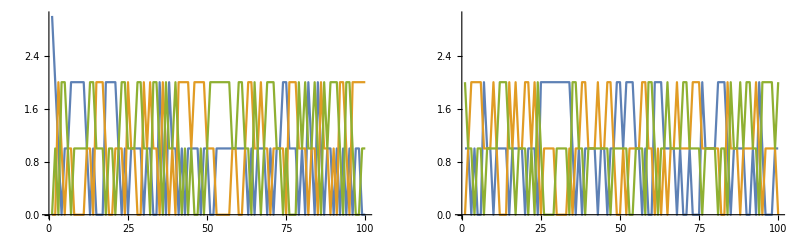

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

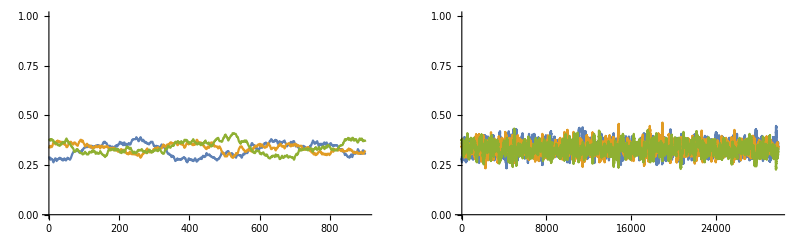

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

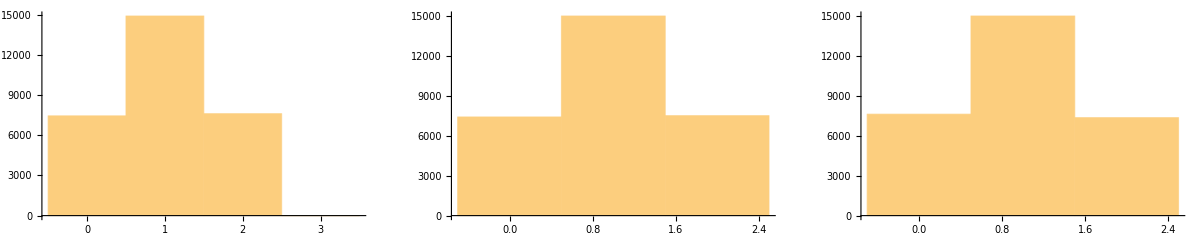

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

```mathematica
Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}]
```

{{1000,1.00.7},{2000,0.90.7},{3000,1.00.7},{4000,1.00.7},{5000,1.00.7},{6000,1.00.7},{7000,1.00.7},{8000,1.00.7},{9000,1.00.7},{10000,1.00.7},{11000,1.00.7},{12000,1.10.7},{13000,1.00.7},{14000,1.00.7},{15000,1.00.7},{16000,1.00.7},{17000,1.00.7},{18000,1.00.7},{19000,1.00.7},{20000,1.00.7},{21000,1.00.7},{22000,1.00.7},{23000,1.00.7},{24000,1.00.7},{25000,1.00.7},{26000,1.00.7},{27000,1.00.7},{28000,1.00.7},{29000,1.00.7},{30000,1.00.7}}

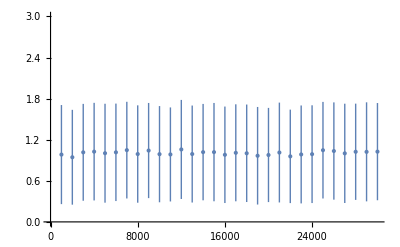

```mathematica
ListPlot[%,PlotRange->{0,3}]
```

## Line

#### No lights - all marbles @ node 1

```mathematica
line=graphToNet[Graph[{1<->2,2<->3}],{3,1}]
```

{{3,{2}},{0,{1,3}},{0,{2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[line,ω,ϕ,30000];
```

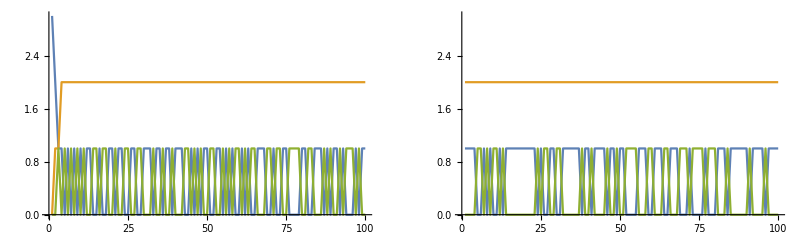

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

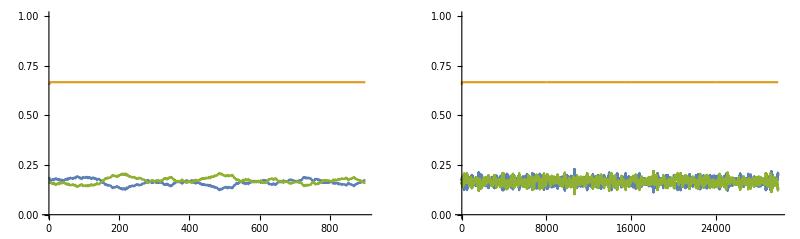

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

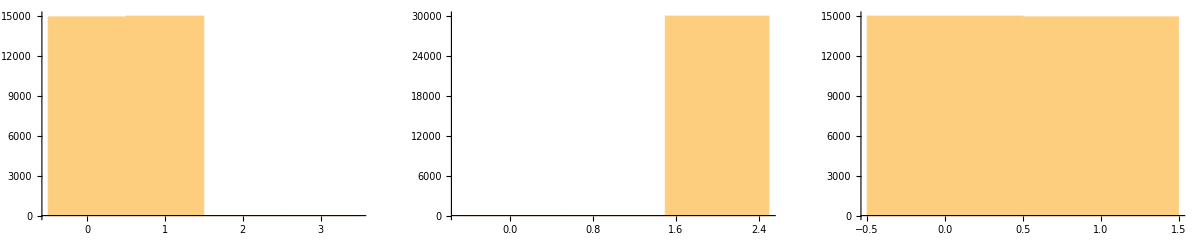

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

```mathematica
devs={Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],Table[{i+1000,Around[Mean[marbles[[All,2]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,2]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],Table[{i+1000,Around[Mean[marbles[[All,3]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,3]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}]};
```

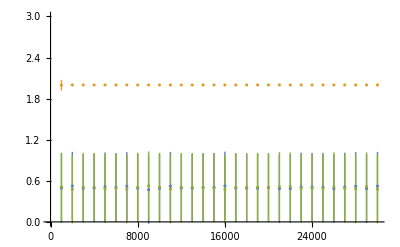

```mathematica
ListPlot[devs,PlotRange->{0,3}]
```

## Complete network

11 nodes, al with degree 10

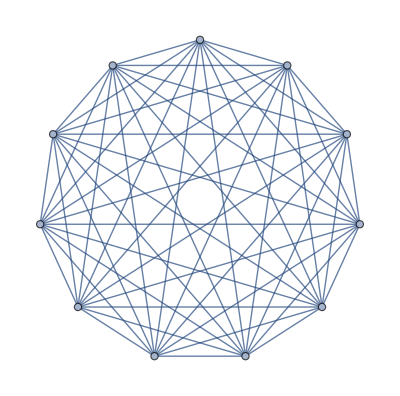

```mathematica
CompleteGraph[11]
```

#### No lights - all marbles @ node 1

```mathematica
complete=graphToNet[CompleteGraph[11],{100,1}]
```

{{100,{2,3,4,5,6,7,8,9,10,11}},{0,{1,3,4,5,6,7,8,9,10,11}},{0,{1,2,4,5,6,7,8,9,10,11}},{0,{1,2,3,5,6,7,8,9,10,11}},{0,{1,2,3,4,6,7,8,9,10,11}},{0,{1,2,3,4,5,7,8,9,10,11}},{0,{1,2,3,4,5,6,8,9,10,11}},{0,{1,2,3,4,5,6,7,9,10,11}},{0,{1,2,3,4,5,6,7,8,10,11}},{0,{1,2,3,4,5,6,7,8,9,11}},{0,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[complete,ω,ϕ,300];
```

```mathematica
marbles//Short
```

{{100,0,0,0,0,0,0,0,0,0,0},«299»,{35,2,12,7,2,23,1,1,1,9,7}}

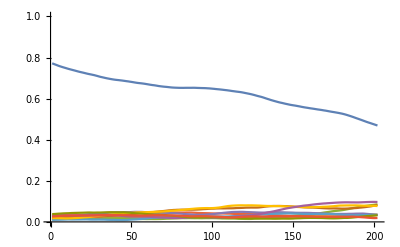

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

#### No lights - marbles all over

```mathematica
complete=graphToNet[CompleteGraph[11],ConstantArray[100,11]]
```

{{100,{2,3,4,5,6,7,8,9,10,11}},{100,{1,3,4,5,6,7,8,9,10,11}},{100,{1,2,4,5,6,7,8,9,10,11}},{100,{1,2,3,5,6,7,8,9,10,11}},{100,{1,2,3,4,6,7,8,9,10,11}},{100,{1,2,3,4,5,7,8,9,10,11}},{100,{1,2,3,4,5,6,8,9,10,11}},{100,{1,2,3,4,5,6,7,9,10,11}},{100,{1,2,3,4,5,6,7,8,10,11}},{100,{1,2,3,4,5,6,7,8,9,11}},{100,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[complete,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100 11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Two dense networks joined by a bridge

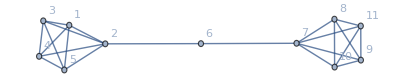

```mathematica
bridgegrapgh=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,4<->5,6<->7,7<->8,7<->9,7<->10,7<->11,8<->9,8<->10,8<->11,9<->10,9<->11,10<->11},VertexLabels->"Name"]
```

#### No lights - all marbles @ node 1

```mathematica
bridge=graphToNet[bridgegrapgh,{100,1}]
```

{{100,{2,3,4,5}},{0,{1,3,4,5,6}},{0,{1,2,4,5}},{0,{1,2,3,5}},{0,{1,2,3,4}},{0,{2,7}},{0,{6,8,9,10,11}},{0,{7,9,10,11}},{0,{7,8,10,11}},{0,{7,8,9,11}},{0,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[bridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
bridge=graphToNet[bridgegrapgh,ConstantArray[100,11]]
```

{{100,{2,3,4,5}},{100,{1,3,4,5,6}},{100,{1,2,4,5}},{100,{1,2,3,5}},{100,{1,2,3,4}},{100,{2,7}},{100,{6,8,9,10,11}},{100,{7,9,10,11}},{100,{7,8,10,11}},{100,{7,8,9,11}},{100,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[bridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100 11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Two sparse networks joined by a bridge

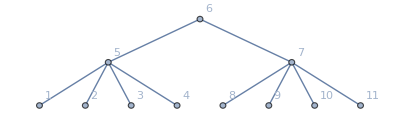

```mathematica
sparsebridgegraph=Graph[{1<->5,2<->5,3<->5,4<->5,5<->6,6<->7,7<->8,7<->9,7<->10,7<->11},VertexLabels->"Name"]
```

#### No lights - all marbles @ node 1

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,{100,1}]
```

{{100,{2}},{0,{1,3,4,5,6}},{0,{2}},{0,{2}},{0,{2}},{0,{2,7}},{0,{6,8,9,10,11}},{0,{7}},{0,{7}},{0,{7}},{0,{7}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[sparsebridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,ConstantArray[100,11]]
```

{{100,{2}},{100,{1,3,4,5,6}},{100,{2}},{100,{2}},{100,{2}},{100,{2,7}},{100,{6,8,9,10,11}},{100,{7}},{100,{7}},{100,{7}},{100,{7}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[sparsebridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100  11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-